# Sum of Lagrange numbers

```mathematica
SetDirectory[NotebookDirectory[]];
markovNums = ReadList["Markov.txt"];
S = 4-GoldenRatio-√2;
c=0.18071710471180647805779264904916762147630562767088273^(-.5);
markovNums[[1000]]
```

60362212372938768121282741975801

```mathematica
sumTo[n_]:=Sum[3-√(9-4/markovNums[[j]]^2),{j,1,n}];
R[n_] := S - sumTo[n];
RLog[n_] := Log[R[n]];
RLog10[n_] := Log10[R[n]];
expectedR[n_] := (6 √n)/c ⅇ^(-2c √n);
expectedRLog[n_] := -2c √n+Log[n]/2+Log[6/c];
expectedRLog10[n_] := (-2c √n)/Log[10]+Log10[n]/2+Log10[6/c];
RLin[n_]:= -RLog[n]+Log[n]/2+Log[6/c];
expectedRLin[n_] := 2c √n;
ⅇ^N[RLog[1000],10]
N[R[1000],10]
```

2.294952×10^-63

2.294951823×10^-63

```mathematica
tableexpectedRLog10 = Table[expectedRLog[n],{n,1,10}];
tableRLog10 = Table[N[RLog[n],10],{n,1,10}];
tableexpectedRLog100 = Table[expectedRLog[n],{n,1,100}];
tableRLog100 = Table[N[RLog[n],10],{n,1,100}];
tableexpectedRLog1000 = Table[expectedRLog[n],{n,1,1000}];
tableRLog1000 = Table[N[RLog[n],10],{n,1,1000}];
```

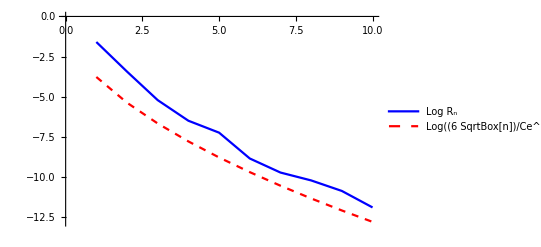

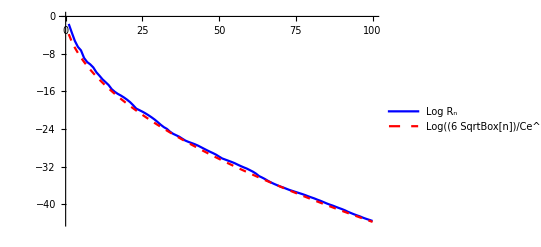

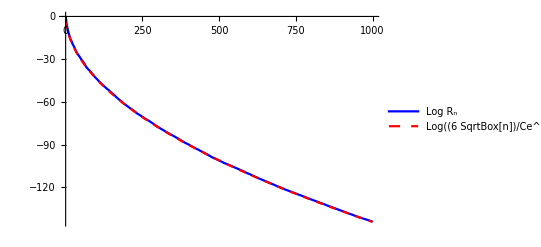

```mathematica
ListLinePlot[{tableRLog10,tableexpectedRLog10},PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"Log R_n","Log((6 SqrtBox[n])/Ce^(-2 C SqrtBox[n]))"}]
ListLinePlot[{tableRLog100,tableexpectedRLog100},PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"Log R_n","Log((6 SqrtBox[n])/Ce^(-2 C SqrtBox[n]))"}]
ListLinePlot[{tableRLog1000,tableexpectedRLog1000},PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"Log R_n","Log((6 SqrtBox[n])/Ce^(-2 C SqrtBox[n]))"}]
```

```mathematica
tableexpectedR100 = Table[N[expectedR[n],10],{n,1,100}];
tableR100 = Table[Exp[N[RLog[n],10]],{n,1,100}];
tableexpectedR1000 = Table[N[expectedR[n],10],{n,1,1000}];
tableR1000 = Table[Exp[N[RLog[n],10]],{n,1,1000}];
```

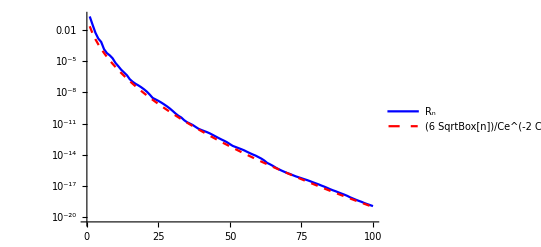

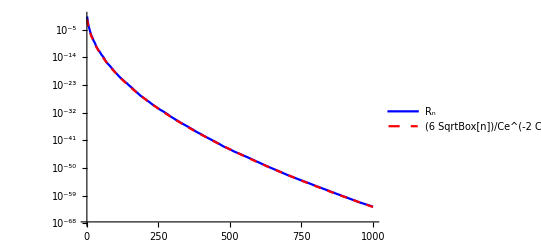

```mathematica
ListLogPlot[{tableR100,tableexpectedR100},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}]
ListLogPlot[{tableR1000,tableexpectedR1000},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}]
```

```mathematica
tableexpectedRLin10 = Table[expectedRLin[n],{n,1,10}];
tableRLin10 = Table[N[RLin[n],10],{n,1,10}];
tableexpectedRLin100 = Table[expectedRLin[n],{n,1,100}];
tableRLin100 = Table[N[RLin[n],10],{n,1,100}];
tableexpectedRLin1000 = Table[expectedRLin[n],{n,1,1000}];
tableRLin1000 = Table[N[RLin[n],10],{n,1,1000}];
```

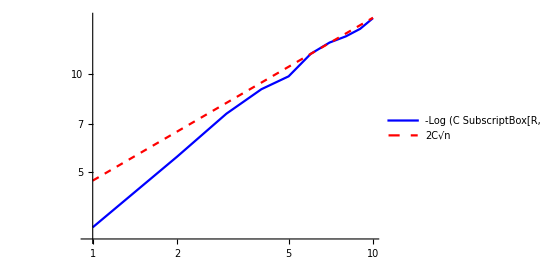

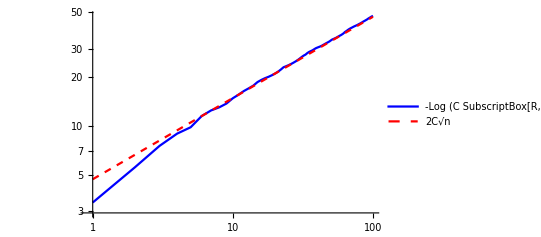

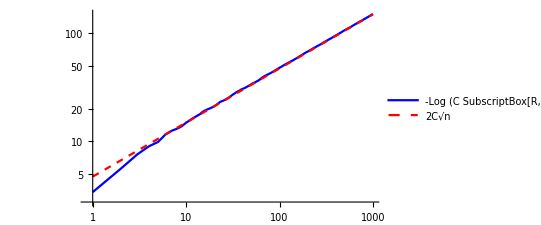

```mathematica
ListLogLogPlot[{tableRLin10,tableexpectedRLin10},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"-Log (C SubscriptBox[R, n])/(6 SqrtBox[n])","2C√n"},AxesOrigin->{0,0},AspectRatio->Automatic, Ticks->{{2,5,10},{
5.0,10.0, 15.0}}]
ListLogLogPlot[{tableRLin100,tableexpectedRLin100},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"-Log (C SubscriptBox[R, n])/(6 SqrtBox[n])","2C√n"},AxesOrigin->{0,0},AspectRatio->Automatic, Ticks->{{2,10,100},{10.0, 20.0, 50.0}}]
ListLogLogPlot[{tableRLin1000,tableexpectedRLin1000},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"-Log (C SubscriptBox[R, n])/(6 SqrtBox[n])","2C√n"},AxesOrigin->{0,0}, AspectRatio->Automatic, Ticks->{{2,10,100, 1000},{10.0, 100.0}}]
```